### ColorData

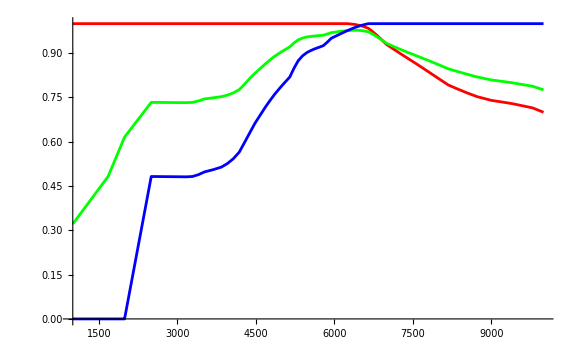

```mathematica
colorPart[fn_, i_] := Function[{x}, fn[x][[i]]]
plotRGBColors[fn_] := plotRGBColors[fn, {0, 1}]
plotRGBColors[fn_, {min_, max_}] := Plot[{
Style[colorPart[fn, 1][x], Red], 
Style[colorPart[fn, 2][x], Green],
Style[colorPart[fn,3][x], Blue]}, {x, min, max}, ImageSize->Large]
plotRGBColors[ColorData["BlackBodySpectrum"], {1000, 10000}]
```

## Modelling

### Mathematica BlackBodySpectrum

#### Data

```mathematica
bb := ColorData["BlackBodySpectrum"];
LinearGradientImage[bb[9000 # + 1000]&]
```

-Graphics-

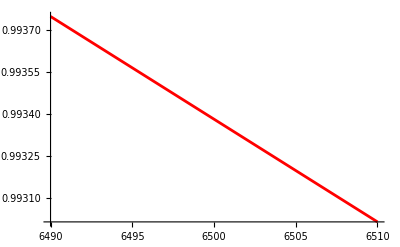
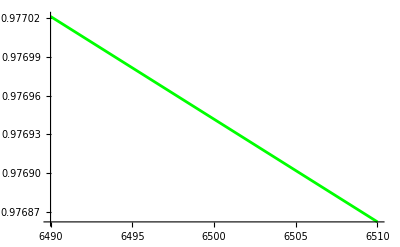
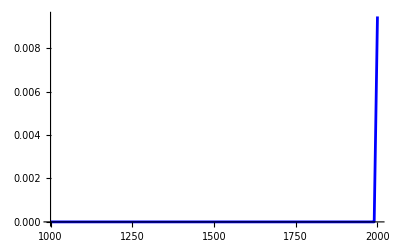
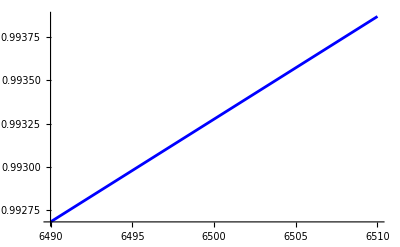
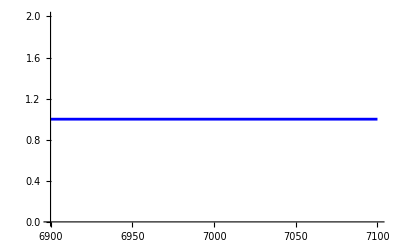
{6500→-Graphics-,6500→-Graphics-,1500→-Graphics-,6500→-Graphics-,7000→-Graphics-}

```mathematica
bbRed[x_] := bb[x][[1]]
bbGreen[x_] := bb[x][[2]]
bbBlue[x_] := bb[x][[3]]
{6500 -> Plot[Style[bbRed[x], Red], {x, 6490, 6510}],
6500 -> Plot[Style[bbGreen[x], Green], {x, 6490, 6510}],
1500 -> Plot[Style[bbBlue[x], Blue], {x, 1000, 2000}],
6500 ->Plot[Style[bbBlue[x], Blue], {x, 6490, 6510}],
7000 -> Plot[Style[bbBlue[x], Blue], {x, 6900, 7100}]
}
```

#### Red

FittedModel[…]

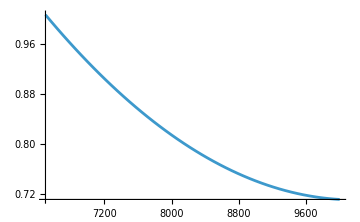
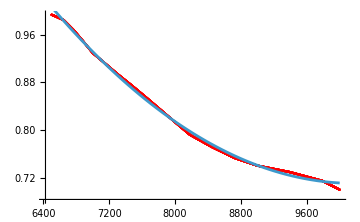
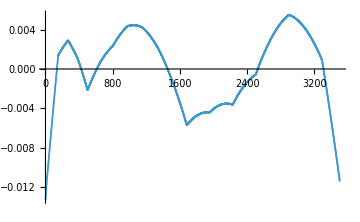

```mathematica
redData0 = {# , bbRed[#]}& /@ Range[6500, 10000, 1];
redFit0 = NonlinearModelFit[redData0, {a + b x + c  x ^2}, {a,b,c},x]
{Plot[redFit0[x], { x, 6500, 10000}, ImageSize->Medium],Show[ListPlot[Style[redData0, Red], ImageSize->Medium], Plot[redFit0[x], { x, 6500, 10000}]],
ListPlot[redFit0["FitResiduals"], ImageSize-> Medium]}
```

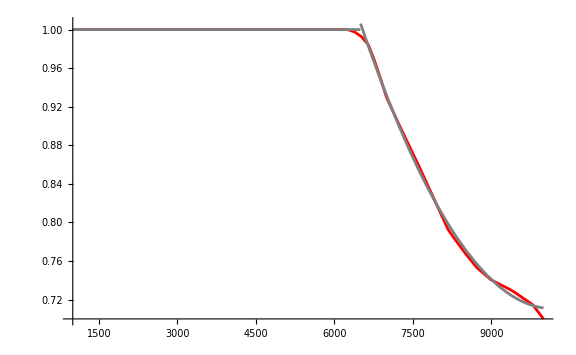

{a→2.97877,b→-0.000445767,c→2.19011×10^-8}

```mathematica
Clear[redFit]
redFit[x_] := Piecewise[{{1, x ≤ 6500}}, redFit0[x]]
Plot[{Style[bbRed[x], Red], Style[redFit[x], Gray]}, {x, 1000, 10000}, ImageSize->Large]
?redFit0
redFit0["BestFitParameters"]
```

#### Green

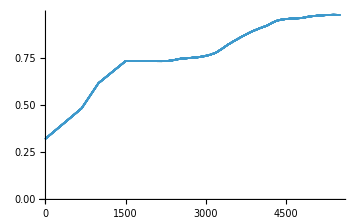
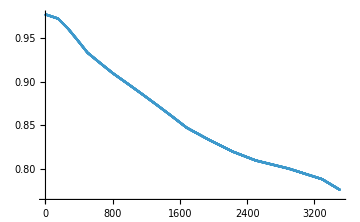

```mathematica
g0 = 1000; g1 = 6500;
gs0 = 1; gs1 = 1;
greenData0 = {#-(g0/gs0), bbGreen[# * gs0]}& /@ Range[g0/gs0 + 1, 6500/ gs0, 1];
greenData1 = {#-(g1 /gs1), bbGreen[# * gs1]}& /@ Range[g1 /gs1+ 1, 10000/ gs1, 1];
{ListPlot[greenData0, ImageSize->Medium],ListPlot[greenData1, ImageSize->Medium]}
```

FittedModel[…]

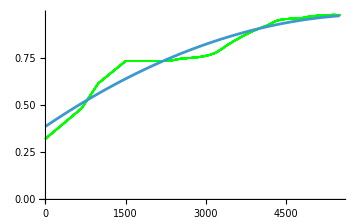
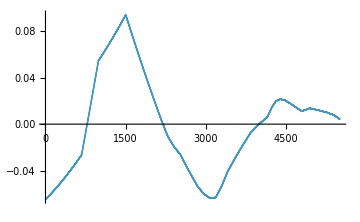

```mathematica
greenData0a = greenData0;
greenFit0 =NonlinearModelFit[greenData0a, {a + b x + c  x ^2}, {a,b,c},x]
{
Show[ListPlot[Style[greenData0, Green], ImageSize->Medium], Plot[greenFit0[x], { x, greenData0[[All, 1]] // Min, greenData0[[All, 1]] // Max}]],
ListPlot[greenFit0["FitResiduals"], ImageSize-> Medium]
}
```

FittedModel[…]

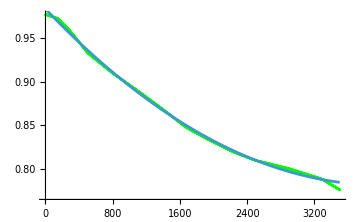
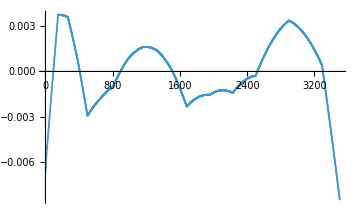

```mathematica
greenFit1 = NonlinearModelFit[greenData1, {a +b x + c x ^2}, {a,b,c}, x]
{
Show[ListPlot[Style[greenData1, Green], ImageSize->Medium], Plot[greenFit1[x], { x, greenData1[[All, 1]] // Min, greenData1[[All, 1]] // Max}]],
ListPlot[greenFit1["FitResiduals"], ImageSize-> Medium]
}
```

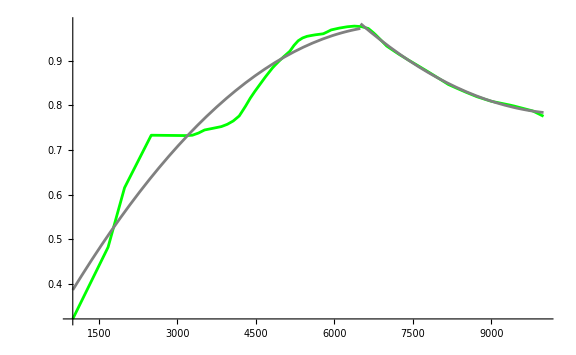

{0.38648,0.000191649,-1.54717×10^-8}

{0.983682,-0.00010113,1.26142×10^-8}

```mathematica
Clear[greenFit]
greenFit[x_] := Piecewise[{{greenFit0[(x-g0) / gs0], x ≤ g1}}, greenFit1[(x-g1) / gs0]]
Plot[{Style[bbGreen[x], Green], Style[greenFit[x], Gray]}, {x, 1000, 10000}, ImageSize->Large]
?greenFit
greenFit0["BestFitParameters"][[All,2]]
greenFit1["BestFitParameters"][[All, 2]]
```

#### Blue

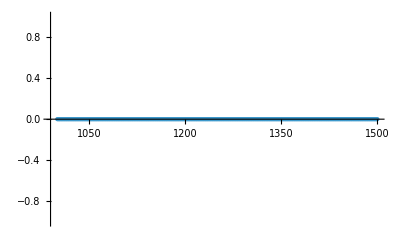
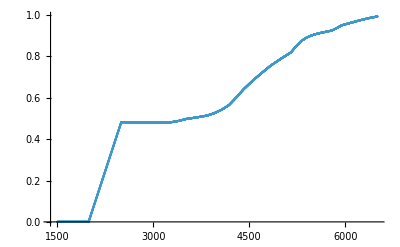
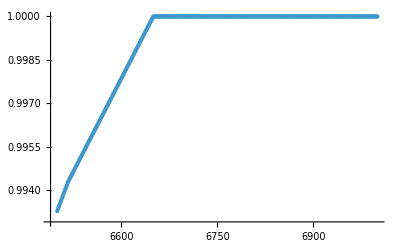
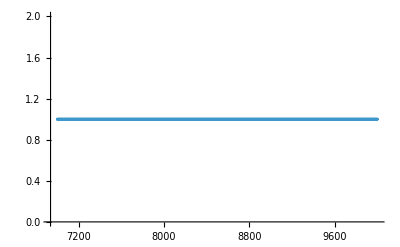

```mathematica
blueData0 = {#, bbBlue[#]}& /@ Range[1000, 1500, 1]; 
blueData1 = {#, bbBlue[#]}& /@ Range[1500, 6500, 1]; 
blueData2 = {#, bbBlue[#]}& /@ Range[6500, 7000, 1];
blueData3 = {#, bbBlue[#]}& /@ Range[7000, 10000, 1];
{ ListPlot[blueData0], ListPlot[blueData1], ListPlot[blueData2], ListPlot[blueData3] }
```

```mathematica
b0 = 1000; b1 = 1500; b2 = 6500; b3 = 7000;
bs0 = 1; bs1 = 1; bs2 = 1; bs3  = 1;
```

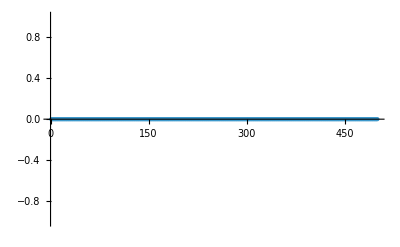

```mathematica
blueData0 = {#-(b0/bs0), bbBlue[# * bs0]}& /@ Range[b0/bs0 + 1, b1/ bs0, 1];
ListPlot[blueData0]
Clear[blueFit0];
blueFit0[x_] := 0
```

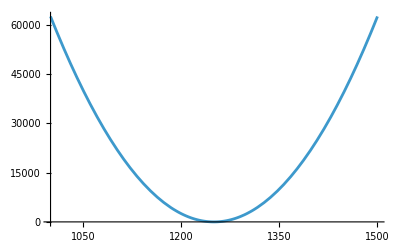

```mathematica
weight1[x_] := (x - Mean[{b0/bs1, b1/bs1}])^2
Plot[weight1[x], {x, b0/bs1, b1/bs1}]
```

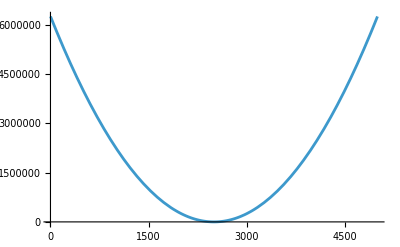

FittedModel[…]

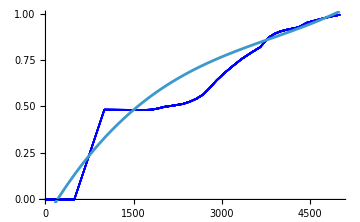
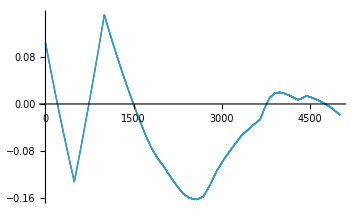

```mathematica
blueData1 = {#-(b1/bs1), bbBlue[# * bs1]}& /@ Range[b1/bs1 + 1, b2/ bs1, 1];
min1 =  blueData1[[All, 1]] // Min;
max1 = blueData1[[All, 1]] // Max;
weight1[x_] := (x - Mean[{min1, max1}])^2
Plot[weight1[x], {x, min1, max1}]
blueFit1 = NonlinearModelFit[blueData1, {a + b x + c x ^2 + d x^3}, {a, b,c, d}, x, Weights-> (weight1[#]&)]
{
Show[ListPlot[Style[blueData1, Blue], ImageSize->Medium], Plot[blueFit1[x], { x,min1, max1}]],
ListPlot[blueFit1["FitResiduals"], ImageSize-> Medium]
}
```

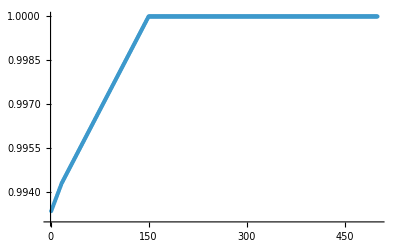

FittedModel[…]

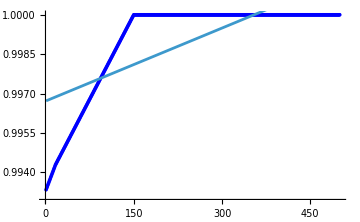
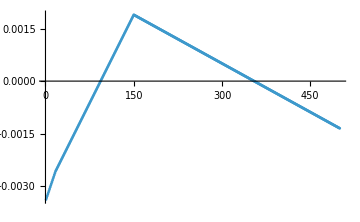

```mathematica
blueData2 = {#-(b2/bs2), bbBlue[# * bs2]}& /@ Range[b2/bs2 + 1, b3/ bs2, 1];
ListPlot[blueData2]
blueFit2 = NonlinearModelFit[blueData2, {a +b x }, {a,b}, x]
{
Show[ListPlot[Style[blueData2, Blue], ImageSize->Medium], Plot[blueFit2[x], { x, blueData2[[All, 1]] // Min, blueData2[[All, 1]] // Max}]],
ListPlot[blueFit2["FitResiduals"], ImageSize-> Medium]
}
```

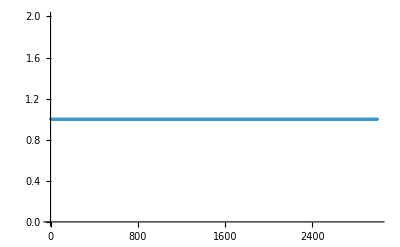

```mathematica
blueData3 = {#-(b3/bs3), bbBlue[# * bs3]}& /@ Range[b3/bs3 + 1, 10000/ bs3, 1];
ListPlot[blueData3]
blueFit3[x_] := 1
```

{1000,1500,6500,7000}

{1,1,1,1}

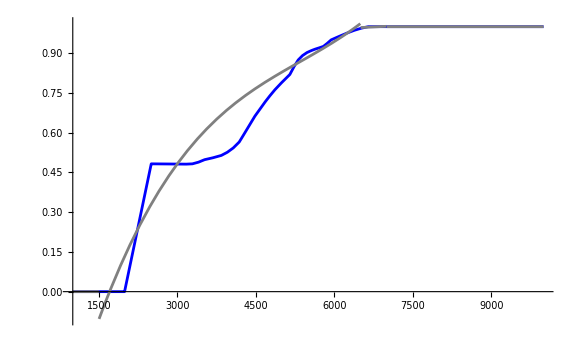

```mathematica
Clear[blueFit]
{b0, b1, b2, b3}
{bs0, bs1, bs2, bs3}
blueFit[x_] := Piecewise[
{
{blueFit0[(x-b0) / bs0], x ≤ b1}, 
{blueFit1[(x-b1) / bs1], x ≤ b2},
{blueFit2[(x-b2) / bs2], x ≤ b3}
}, 
blueFit3[(x-b3) / bs3]
]
Plot[{Style[bbBlue[x], Blue], Style[blueFit[x], Gray]}, {x, 1000, 10000}, ImageSize->Large]
```

```mathematica
blueFit1["BestFitParameters"]
blueFit2["BestFitParameters"]
```

{a→-0.104452,b→0.000535392,c→-1.10297×10^-7,d→9.5739×10^-12}

{a→0.996711,b→9.27878×10^-6}

#### All

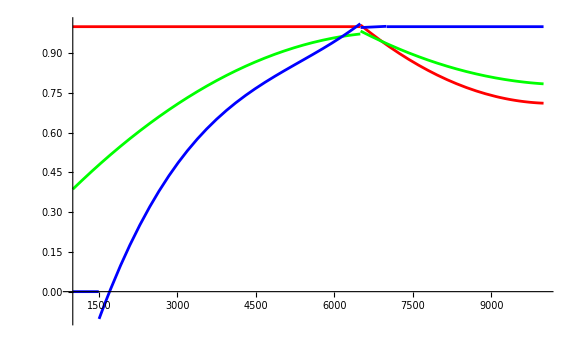

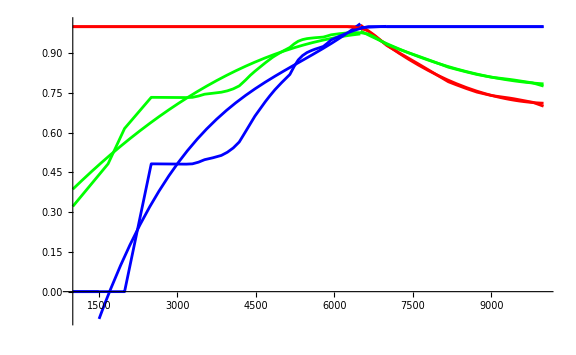

```mathematica
plot1 = Plot[{Style[redFit[x], Red], Style[greenFit[x], Green], Style[blueFit[x], Blue]}, {x, 1000, 10000}, ImageSize->Large]
Show[plot1, plotRGBColors[bb, {1000, 10000}]]
```

## Mitchell Charity

### Data

From here: http://www.vendian.org/mncharity/dir3/blackbody/UnstableURLs/bbr_color.html

```mathematica
charity =  Import[NotebookDirectory[] <> "Mitchell Charity.xlsx"][[1]];
charity = charity[[2;;All]];
tenDeg = Select[charity, #[[2]]=="10deg"&];
twoDeg = Select[charity, #[[2]]=="2deg"&];
{Dimensions[charity], Dimensions[tenDeg], Dimensions[twoDeg]}
```

{{782,12},{391,12},{391,12}}

```mathematica
charityColorData= {tenDeg[[All, {1}]],tenDeg[[All, {6, 7, 8}]]}// Transpose;
charityColorData = Interpolation[charityColorData, InterpolationOrder->3]
charityColor[kelvin_] := RGBColor @@ charityColorData[kelvin]
charityColorData[2550] * 255
charityColorNormal[level_] := charityColor[9000 level + 1000]
LinearGradientImage[charityColorNormal]
```

InterpolatingFunction[…]

{255.,93.8894,18.199}

-Graphics-

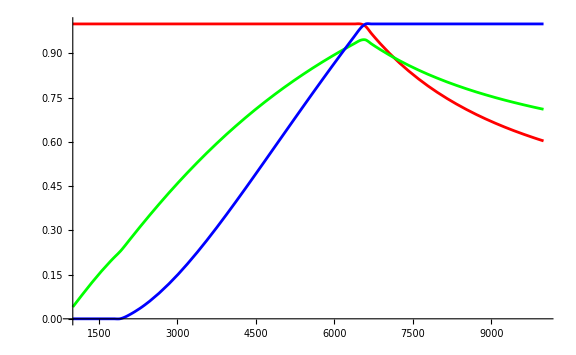

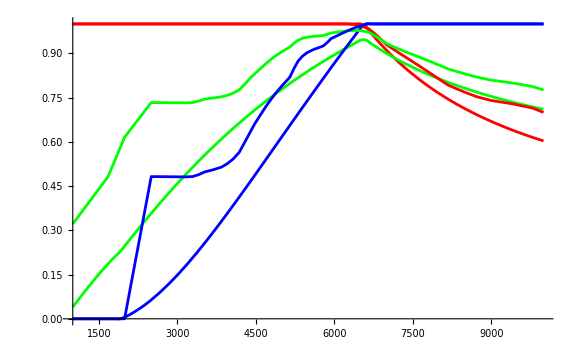

```mathematica
plotRGBColors[charityColor, {1000, 10000}]
Show[plotRGBColors[charityColor, {1000, 10000}],plotRGBColors[bb, {1000, 10000}]]
```

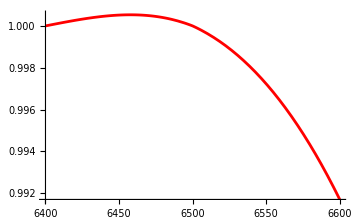
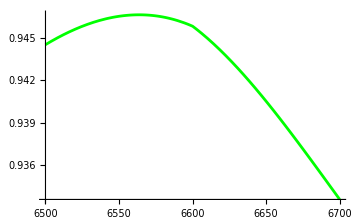
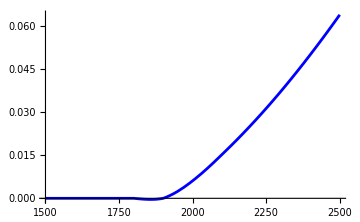
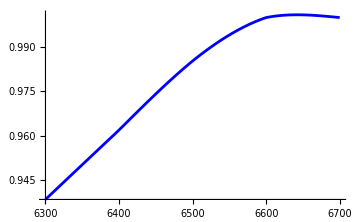
{6500→-Graphics-,6600→-Graphics-,2000→-Graphics-,6600→-Graphics-}

```mathematica
ccRed[x_] := charityColor[x][[1]]
ccGreen[x_] := charityColor[x][[2]]
ccBlue[x_] := charityColor[x][[3]]
{6500 -> Plot[Style[ccRed[x], Red], {x, 6400, 6600}, ImageSize->Medium],
6600 -> Plot[Style[ccGreen[x], Green], {x, 6500, 6700},ImageSize->Medium],
2000 -> Plot[Style[ccBlue[x], Blue], {x, 1500, 2500},ImageSize->Medium],
6600 ->Plot[Style[ccBlue[x], Blue], {x, 6300, 6700},ImageSize->Medium]
}
```

### Piecewise

#### Red

{6500,10000}

6500

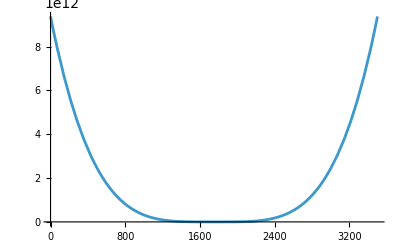

FittedModel[…]

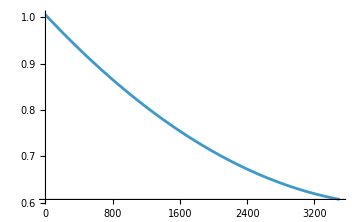
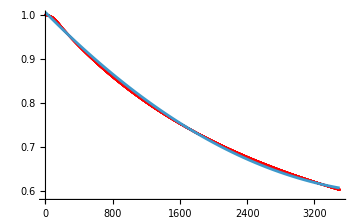
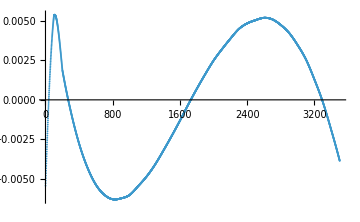

```mathematica
range = {6500, 10000}
r0 = range[[1]]
sRange = (range - r0);
xRange = {x} ~Join~ sRange;
(*weight[x_] := ((sRange[[2]] - x) / (sRange[[2]] - sRange[[1]])) ^ 2*)
weight[x_] := Abs[x - Mean[sRange]]^4
Plot[weight[x], xRange]
redData0 = {#-range[[1]] , ccRed[#]}& /@ (Range@@range);
ListPlot[Style[redData0, Red]];
redFit0 = NonlinearModelFit[redData0, {a + b x + c  x ^2}, {a,b,c},x, Weights-> (weight[#]&)]
{Plot[redFit0[x], xRange, ImageSize->Medium],Show[ListPlot[Style[redData0, Red], ImageSize->Medium], Plot[redFit0[x], xRange]],
ListPlot[redFit0["FitResiduals"], ImageSize-> Medium]}
```

{6500,10000}

{a→1.00545,b→-0.000193196,c→2.26863×10^-8}

InterpolatingFunction::dmval: 输入值 {0.204286} 位于插值函数的数据范围之外. 将使用外推法.

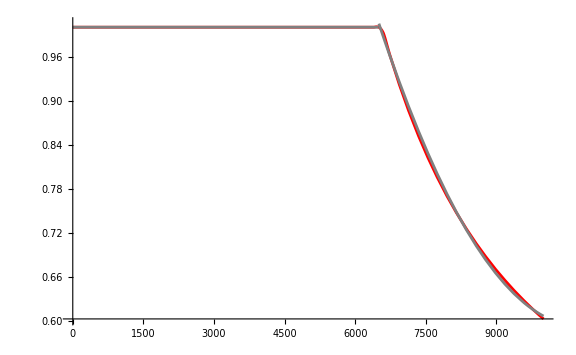

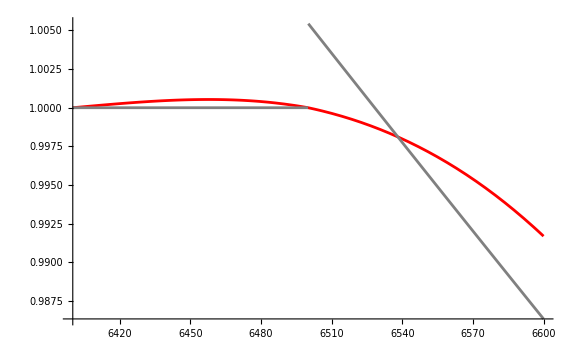

```mathematica
Clear[redFit]
range
redFit0["BestFitParameters"]
redFit[x_] := Piecewise[{{1, x ≤ range[[1]]}}, redFit0[x-range[[1]]]]
Plot[{Style[ccRed[x], Red], Style[redFit[x], Gray]}, {x, 0, 10000}, ImageSize->Large]
Plot[{Style[ccRed[x], Red], Style[redFit[x], Gray]}, {x, 6400, 6600}, ImageSize->Large]
```

#### Green

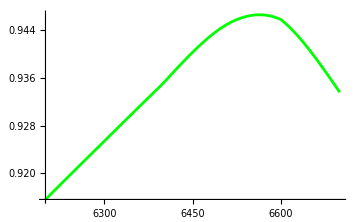
6600→-Graphics-

```mathematica
6600 -> Plot[Style[ccGreen[x], Green], {x, 6200, 6700},ImageSize->Medium]
```

{x,0,5500}

{x,0,100}

{x,0,3400}

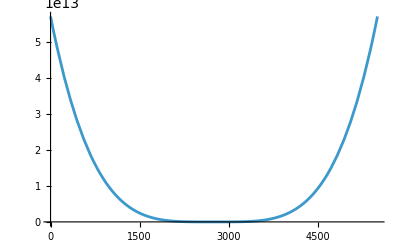

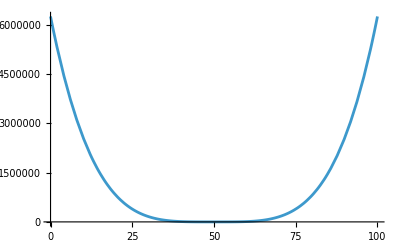

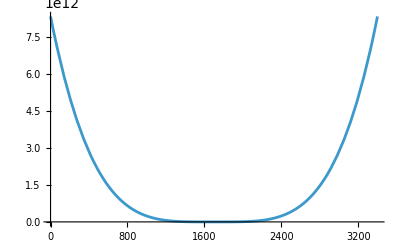

```mathematica
range0 = {1000, 6500}; sRange0 = (range0 - range0[[1]]);
range1 = {6500, 6600}; sRange1 = (range1 - range1[[1]]);
range2 = {6600, 10000}; sRange2 = (range2 - range2[[1]]);

xRange0 = {x} ~Join~ sRange0
xRange1 = {x} ~Join~ sRange1
xRange2 = {x} ~Join~ sRange2
weight0[x_] := Abs[x - Mean[sRange0]]^4
weight1[x_] := Abs[x - Mean[sRange1]]^4
weight2[x_] := Abs[x - Mean[sRange2]]^4
Plot[weight0[x], xRange0]
Plot[weight1[x], xRange1]
Plot[weight2[x], xRange2]
```

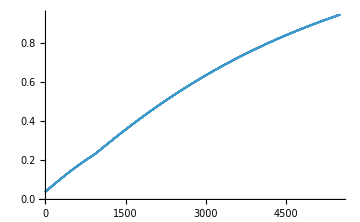
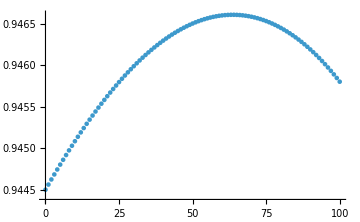
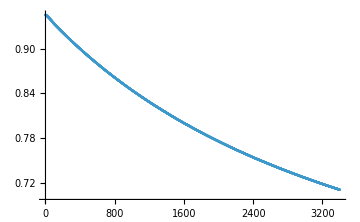

```mathematica
g0 = range0[[1]]; g1 = range1[[1]]; g2 = range2[[1]];
greenData0 = {#-g0, ccGreen[#]}& /@ Range[g0, g1, 1];
greenData1 = {#-g1 , ccGreen[#]}& /@ Range[g1, g2, 1];
greenData2 = {#-g2 , ccGreen[#]}& /@ Range[g2, 10000, 1];
{ListPlot[greenData0, ImageSize->Medium],ListPlot[greenData1, ImageSize->Medium], ListPlot[greenData2, ImageSize->Medium]}
```

FittedModel[…]

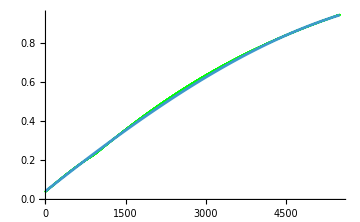
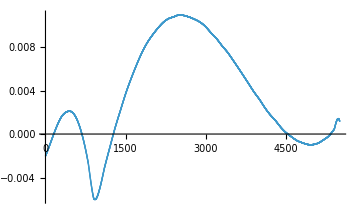

```mathematica
greenFit0 =NonlinearModelFit[greenData0, {a + b x + c  x ^2 + d x^3}, {a,b,c, d},x, Weights-> (weight0[#]&)]
{
Show[ListPlot[Style[greenData0, Green], ImageSize->Medium], Plot[greenFit0[x], xRange0]],
ListPlot[greenFit0["FitResiduals"], ImageSize-> Medium]
}
```

FittedModel[…]

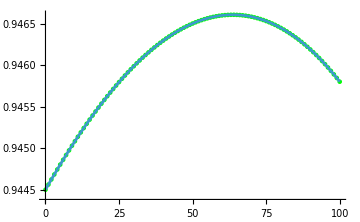
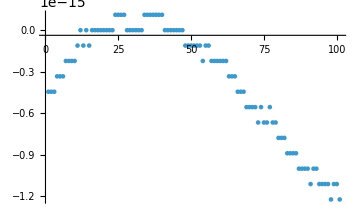

```mathematica
greenFit1 = NonlinearModelFit[greenData1, {a + b x + c  x ^2 + d x^3}, {a,b,c, d}, x, Weights-> (weight1[#]&)]
{
Show[ListPlot[Style[greenData1, Green], ImageSize->Medium], Plot[greenFit1[x], xRange1]],
ListPlot[greenFit1["FitResiduals"], ImageSize-> Medium]
}
```

FittedModel[…]

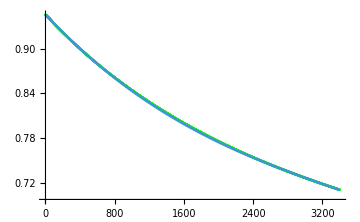
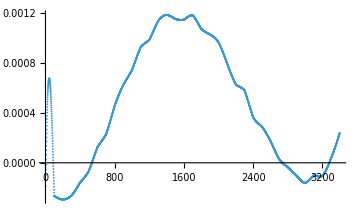

```mathematica
greenFit2 = NonlinearModelFit[greenData2, {a + b x + c  x ^2 + d x^3}, {a,b,c, d}, x, Weights-> (weight2[#]&)]
{
Show[ListPlot[Style[greenData2, Green], ImageSize->Medium], Plot[greenFit2[x], xRange2]],
ListPlot[greenFit2["FitResiduals"], ImageSize-> Medium]
}
```

{1000,6500,6600}

{0.0421145,0.000217582,-5.21559×10^-9,-8.2771×10^-13}

{0.9445,0.0000625,-4.05×10^-7,-9.×10^-10}

{0.945986,-0.000123522,2.32367×10^-8,-2.14392×10^-12}

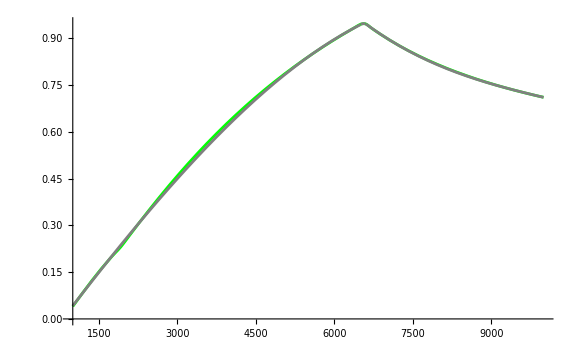

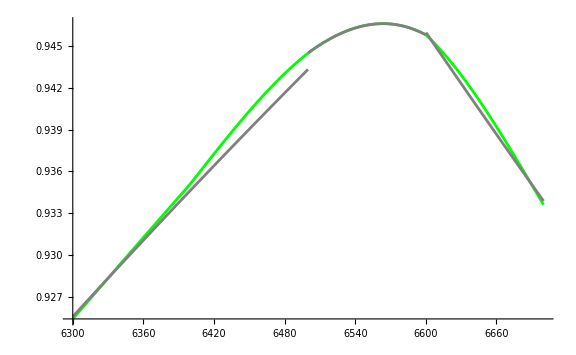

```mathematica
Clear[greenFit]
{ g0 , g1, g2}
greenFit0["BestFitParameters"][[All,2]]
greenFit1["BestFitParameters"][[All, 2]]
greenFit2["BestFitParameters"][[All, 2]]
greenFit[x_] := Piecewise[{{greenFit0[x-g0], x ≤ g1}, {greenFit1[x-g1], x ≤ g2}}, greenFit2[x-g2]]
Plot[{Style[ccGreen[x], Green], Style[greenFit[x], Gray]}, {x, 1000, 10000}, ImageSize->Large]
Plot[{Style[ccGreen[x], Green], Style[greenFit[x], Gray]}, {x, 6300, 6700}, ImageSize->Large]
```

#### Blue

```mathematica
{2000 -> Plot[Style[ccBlue[x], Blue], {x, 1500, 2500},ImageSize->Medium],
6600 ->Plot[Style[ccBlue[x], Blue], {x, 6300, 6700},ImageSize->Medium]}
```

{2000→-Graphics-,6600→-Graphics-}

{x,0,900}

{x,0,4700}

{x,0,3400}

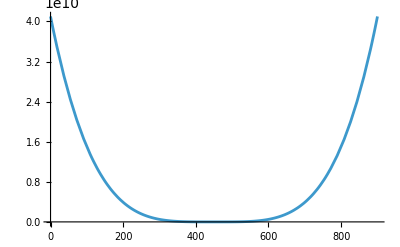

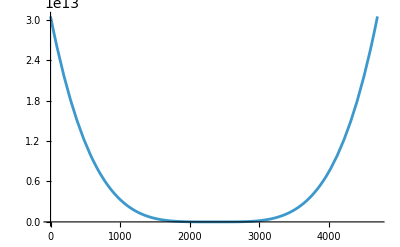

-Graphics-

```mathematica
range0 = {1000, 1900}; sRange0 = (range0 - range0[[1]]);
range1 = {range0[[2]], 6600}; sRange1 = (range1 - range1[[1]]);
range2 = {range1[[2]], 10000}; sRange2 = (range2 - range2[[1]]);

xRange0 = {x} ~Join~ sRange0
xRange1 = {x} ~Join~ sRange1
xRange2 = {x} ~Join~ sRange2
weight0[x_] := Abs[x - Mean[sRange0]]^4
weight1[x_] := Abs[x - Mean[sRange1]]^4
weight2[x_] := Abs[x - Mean[sRange2]]^4
Plot[weight0[x], xRange0]
Plot[weight1[x], xRange1]
Plot[weight2[x], xRange2]
```

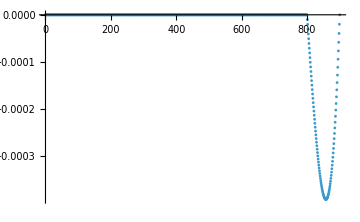
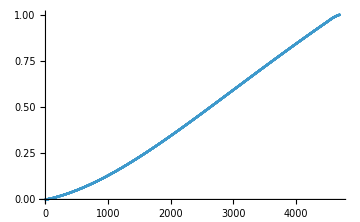
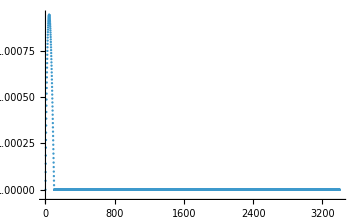

```mathematica
b0 = range0[[1]]; b1 = range1[[1]]; b2 = range2[[1]];
blueData0 = {#-b0, ccBlue[#]}& /@ Range[b0, b1, 1];
blueData1 = {#-b1 , ccBlue[#]}& /@ Range[b1, b2, 1];
blueData2 = {#-b2 , ccBlue[#]}& /@ Range[b2, 10000, 1];
{ListPlot[blueData0, ImageSize->Medium],ListPlot[blueData1, ImageSize->Medium], ListPlot[blueData2, ImageSize->Medium]}
```

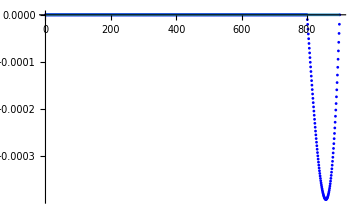

```mathematica
Clear[blueFit0]
blueFit0[x_] := 0
(*blueFit0 =NonlinearModelFit[blueData0, {a + b x }, {a,b},x, Weights-> (weight0[#]&)]*)
{
Show[ListPlot[Style[blueData0, Blue], ImageSize->Medium], Plot[blueFit0[x], xRange0]](*,
ListPlot[blueFit0["FitResiduals"], ImageSize-> Medium]*)
}
```

FittedModel[…]

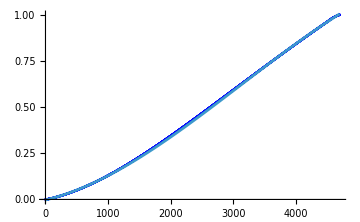
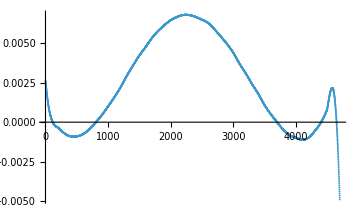

```mathematica
blueFit1 = NonlinearModelFit[blueData1, {a + b x + c  x ^2 + d x^3}, {a,b,c, d}, x, Weights-> (weight1[#]&)]
{
Show[ListPlot[Style[blueData1, Blue], ImageSize->Medium], Plot[blueFit1[x], xRange1]],
ListPlot[blueFit1["FitResiduals"], ImageSize-> Medium]
}
```

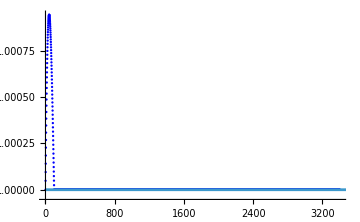

```mathematica
Clear[blueFit2]
blueFit2[x_] := 1
{
Show[ListPlot[Style[blueData2, Blue], ImageSize->Medium], Plot[blueFit2[x], xRange1]]
}
```

{1000,1900,6600}

{a→-0.0026298,b→0.0000801242,c→5.73172×10^-8,d→-6.11809×10^-12}

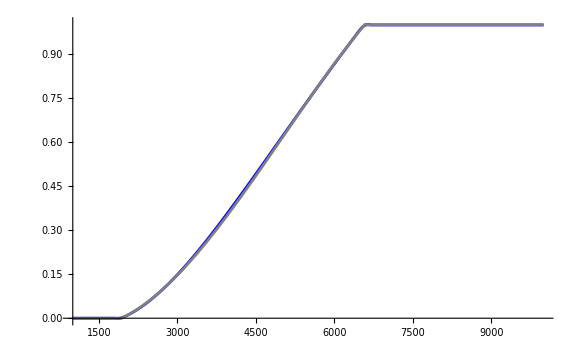

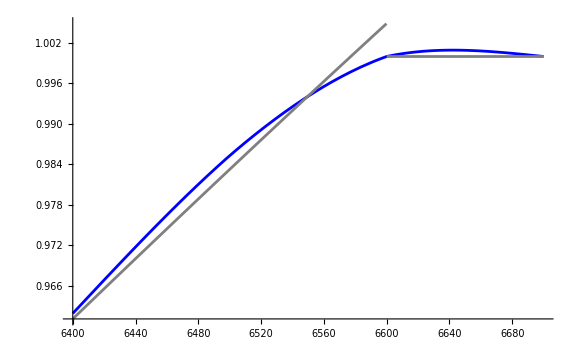

```mathematica
Clear[blueFit]
{b0, b1, b2}
blueFit1["BestFitParameters"]
blueFit[x_] := Piecewise[
{
{blueFit0[x-b0], x ≤ b1}, 
{blueFit1[x-b1], x ≤ b2}
}, 
blueFit2[x-b2]
]
Plot[{Style[ccBlue[x], Blue], Style[blueFit[x], Gray]}, {x, 1000, 10000}, ImageSize->Large]
Plot[{Style[ccBlue[x], Blue], Style[blueFit[x], Gray]}, {x, 6400, 6700}, ImageSize->Large]
```

### Holistic

#### Prolog

It’s actually a much better idea if we throw the whole function at NonlinearModelFit so that it sees the pieces and can fit across same.

```mathematica
shiftQuad[dx_] := a + b (x-dx) + c  (x-dx) ^2
shiftCubic[dx_] := a + b (x-dx) + c  (x-dx) ^2 +  d  (x-dx) ^3
shiftCubic2[dx_] := e + f (x-dx) + g  (x-dx) ^2 +  h  (x-dx) ^3
```

#### Red

Piecewise[{{1, x≤6500}, {a+b (-6500+x)+c (-6500+x)^2, True}}]

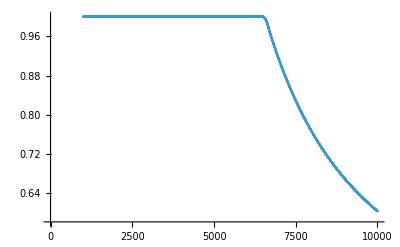

```mathematica
redForm = Piecewise[
{{1, x ≤ r0}},
shiftQuad[r0]]
redData = {# , ccRed[#]}& /@ Range[1000, 10000];
ListPlot[redData]
```

FittedModel[…]

{a→1.0018,b→-0.000191353,c→2.27577×10^-8}

InterpolatingFunction::dmval: 输入值 {0.204286} 位于插值函数的数据范围之外. 将使用外推法.

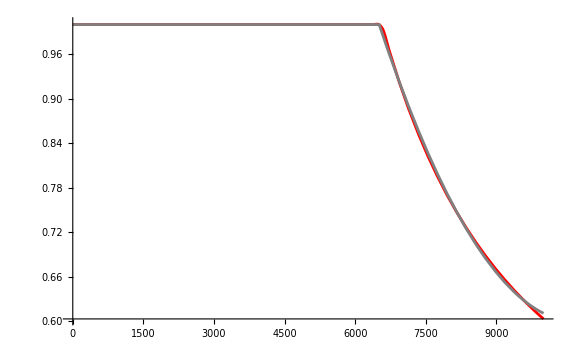

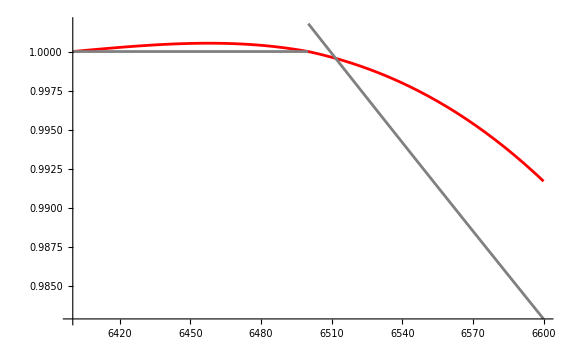

```mathematica
redFit = NonlinearModelFit[redData, redForm, {a,b,c},x]
redFit["BestFitParameters"]
Plot[{Style[ccRed[x], Red], Style[redFit[x], Gray]}, {x, 0, 10000}, ImageSize->Large]
Plot[{Style[ccRed[x], Red], Style[redFit[x], Gray]}, {x, 6400, 6600}, ImageSize->Large]
```

#### Green

```mathematica
{g0, g2 }
```

{1000,6600}

Piecewise[{{a+b (-1000+x)+c (-1000+x)^2+d (-1000+x)^3, x≤6600}, {e+f (-6600+x)+g (-6600+x)^2+h (-6600+x)^3, True}}]

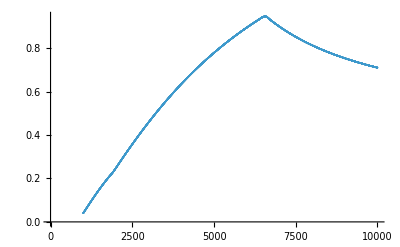

```mathematica
greenForm = Piecewise[
{
{shiftCubic[g0], x ≤ g2}
},
shiftCubic2[g2]]
greenData = {# , ccGreen[#]}& /@ Range[1000, 10000];
ListPlot[greenData]
```

```mathematica
greenFit = NonlinearModelFit[greenData, greenForm, {a,b,c, d, e, f, g, h},x]
```

FittedModel[…]

{a→0.0374325,b→0.00022692,c→-7.0972×10^-9,d→-7.87688×10^-13,e→0.945357,f→-0.000121171,g→2.21965×10^-8,h→-2.03433×10^-12}

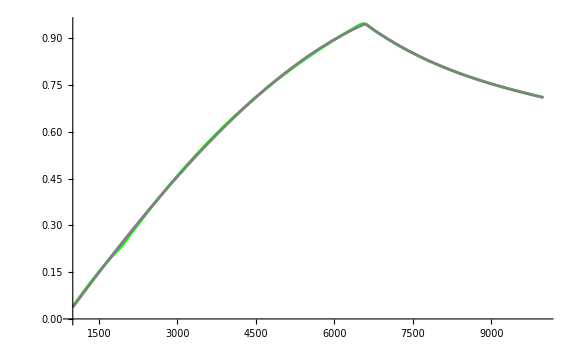

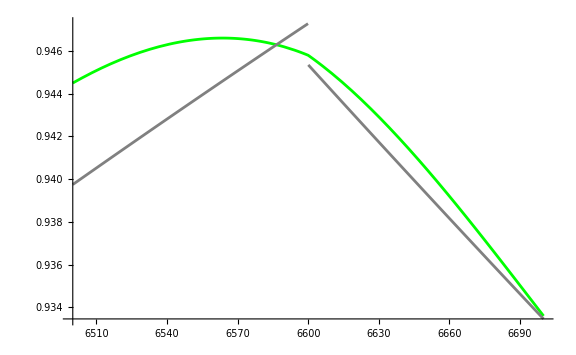

```mathematica
greenFit["BestFitParameters"]
Plot[{Style[ccGreen[x], Green], Style[greenFit[x], Gray]}, {x, 1000, 10000}, ImageSize->Large]
Plot[{Style[ccGreen[x], Green], Style[greenFit[x], Gray]}, {x, 6500, 6700}, ImageSize->Large]
```

#### Blue

```mathematica
{ b1, b2 }
```

{1900,6600}

Piecewise[{{0, x≤1900}, {a+b (-1900+x)+c (-1900+x)^2+d (-1900+x)^3, x≤6600}, {1, True}}]

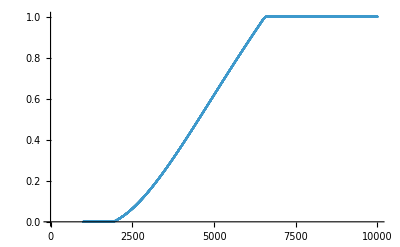

```mathematica
blueForm = Piecewise[
{{0, x ≤ b1}, 
{shiftCubic[b1], x ≤ b2}},
1]
blueData = {# , ccBlue[#]}& /@ Range[1000, 10000];
ListPlot[blueData]
```

```mathematica
blueFit = NonlinearModelFit[blueData, blueForm, {a,b,c, d},x]
```

FittedModel[…]

```mathematica
blueFit["BestFitParameters"]
```

{a→-0.0058959,b→0.0000885465,c→5.48613×10^-8,d→-5.96726×10^-12}

InterpolatingFunction::dmval: 输入值 {0.204286} 位于插值函数的数据范围之外. 将使用外推法.

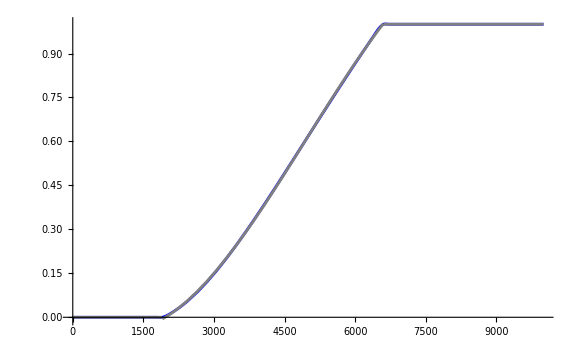

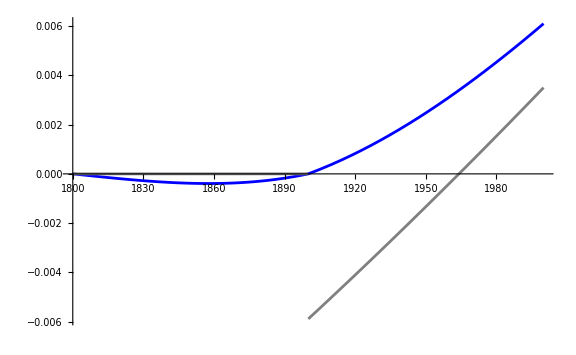

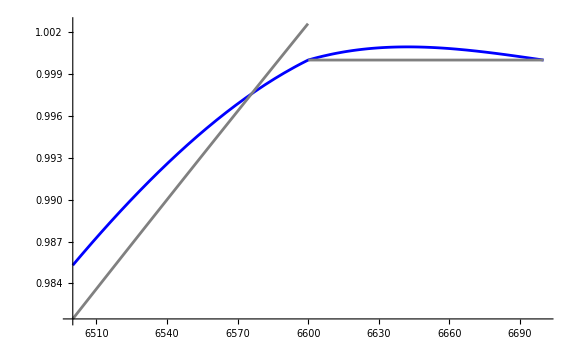

```mathematica
Plot[{Style[ccBlue[x], Blue], Style[blueFit[x], Gray]}, {x, 0, 10000}, ImageSize->Large]
Plot[{Style[ccBlue[x], Blue], Style[blueFit[x], Gray]}, {x, 1800, 2000}, ImageSize->Large]
Plot[{Style[ccBlue[x], Blue], Style[blueFit[x], Gray]}, {x, 6500, 6700}, ImageSize->Large]
```

#### All

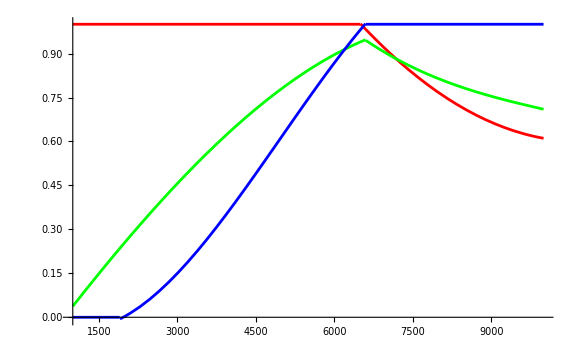

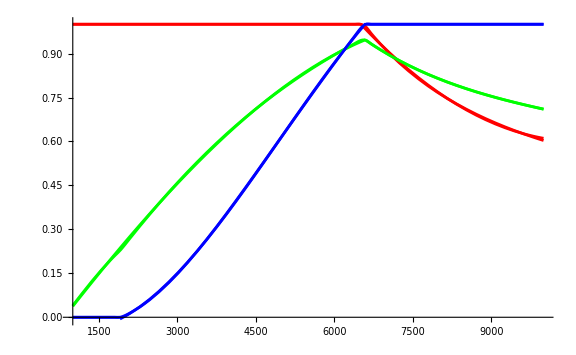

```mathematica
plot2 = Plot[{Style[redFit[x], Red], Style[greenFit[x], Green], Style[blueFit[x], Blue]}, {x, 1000, 10000}, ImageSize->Large]
Show[plot2, plotRGBColors[charityColor, {1000, 10000}]]
```